1.

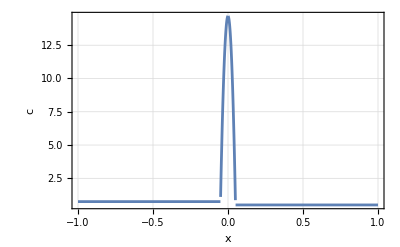

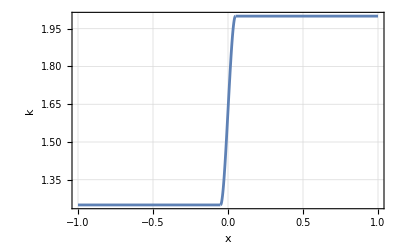

```mathematica
Clear["Global`*"]
T1=-1;
T2=2;
l=1;
lambda=1;
tmax=1;
tau=0.01;
n=100;
h=l/n;
delta=0.05;
k1=1.25;
k2=2;
c1=0.75;
c2=0.5;
kappa1=k1/c1;
kappa2=k2/c2;

alpha=alpha/.FindRoot[(k1/(√(Pi*kappa1))*T1/Erf[alpha/(2 √kappa1)]*Exp[-alpha^2/(4kappa1)]+k2/(√(Pi*kappa2))*T2/(1-Erf[alpha/(2 √kappa2)])*Exp[-alpha^2/(4kappa2)])==-(alpha*lambda)/2,{alpha,1}];
A1=T1;B1=-T1/Erf[alpha/(2 √kappa1)];
A2=-T2 Erf[alpha/(2 √kappa2)]/(1-Erf[alpha/(2 √kappa2)]);  B2=T2*1/(1-Erf[alpha/(2 √kappa2)]);
ksi[t_]:=alpha √t;
(*Task 1*)
Uex[x_,t_]:=Piecewise[
{{A1+B1*Erf[x/(2 √(kappa1*(t+0.00000000000001)))],0<=x<ksi[t]},
{A2+B2*Erf[x/(2 √(kappa2*(t+0.00000000000001)))],x>=ksi[t]}}];
(*Task 2*)
f[x_,t_]:=0;
u0[x_]:=T2;
mu1[t_]:=T1;
mu2[t_]:=Uex[l,t];
cf=LinearSolve[{{1,0,delta^2},{1,delta^2,0},{2delta,delta^3/3,delta^3/3}},{c2/lambda,c1/lambda,1}];
c[x_]:=Piecewise[{
{c1,x<-delta},{c2,x>delta},{cf[[1]]+cf[[2]]x^2 ,-delta<=x<=0},{cf[[1]]+cf[[3]]x^2 ,0<=x<=delta}
}];
(*{x,-delta,delta}*)
Integrate[c[x],{x,-delta,delta}]
Plot[c[x],{x,-l,l},FrameStyle->Directive[Black,12],PlotRange->All,Frame->True,FrameLabel->{Style["x",16,Black,FontFamily->"Cambria"],Style["c",16,Black,FontFamily->"Cambria"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->All]
ks[x_]:=a0+a1*x+a2*x^2+a3*x^3;
ks[x_]=(a0+a1*x+a2*x^2+a3*x^3)/.Solve[{ks[delta]==k2,ks[-delta]==k1,ks'[delta]==0,ks'[-delta]==0},{a0,a1,a2,a3}][[1]];
k[x_]:=Piecewise[{
{k1,x<-delta},{k2,x>delta},{ks[x],-delta<=x<=delta}
}];
Plot[k[x],{x,-l,l},FrameStyle->Directive[Black,12],PlotRange->All,Frame->True,FrameLabel->{Style["x",16,Black,FontFamily->"Cambria"],Style["k",16,Black,FontFamily->"Cambria"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->All]
Stephan[f_,u1_,u2_,u0_,l_,T_,h_,tau_,eps_]:=Module[{sm,xlist,tlist,mui,phiV,sol,exact,Ly,mtr,b,M,un,uns},
ErrList={};
IterList={};
sm=T/tau;
xlist=Table[i*h,{i,0,n}];
tlist=Table[s*tau,{s,0.,sm}];
sol=Table[0,{s,0,sm},{i,0,n}];
Do[sol[[1,i]]=u0[xlist[[i]]],{i,1,n+1}];
Do[sol[[s,1]]=u1[tlist[[s]]],{s,1,sm+1}];
Do[sol[[s,n+1]]=u2[tlist[[s]]],{s,1,sm+1}];
Do[
itr=0;
un=Table[sol[[s,i]],{i,1,n+1}];
b=Table[0,{i,0,n}];b[[1]]=sol[[s+1,1]];b[[n+1]]=sol[[s+1,n+1]];
M=Table[0,{s,0,sm},{i,0,n}];M[[1,1]]=1;M[[n+1,n+1]]=1;
err=10;
While[err>eps,
itr+=1;
Do[
M[[i,i-1]]=-1/h^2*(k[un[[i]]]+k[un[[i-1]]])/2;
M[[i,i]]=c[un[[i]]]/tau+1/h^2*(k[un[[i]]]+k[un[[i+1]]])/2+1/h^2*(k[un[[i]]]+k[un[[i-1]]])/2;
M[[i,i+1]]=-1/h^2*(k[un[[i]]]+k[un[[i+1]]])/2;
b[[i]]=f[xlist[[i]],tlist[[s+1]]]+c[un[[i]]]/tau*un[[i]],
{i,2,n}];
uns=LinearSolve[M,b];
(*Print[uns];*)
err=Max[Abs[uns-un]];
un=uns;
];
AppendTo[IterList,{s,itr}];
AppendTo[ErrList,{s,err}];
Do[sol[[s+1,i]]=un[[i]],{i,1,n+1}]
,{s,1,sm}];
Return[{sol,IterList,ErrList}];
];
{sol,IterList,ErrList}=Stephan[f,mu1,mu2,u0,l,tmax,h,tau,0.0001];
```

-Graphics3D-

-Graphics3D-

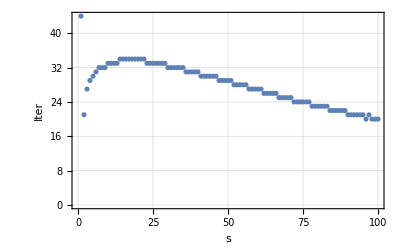

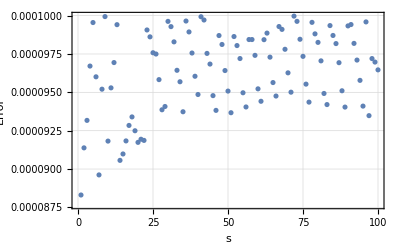

```mathematica
Plot3D[Uex[x,t],{x,0,l},{t,0,1},ColorFunction->"TemperatureMap"]
U={};
Do[AppendTo[U,{i*h,s*tau,sol[[s+1,i+1]]}],{s,0,tmax/tau},{i,0,n}]
ListPlot3D[U,ColorFunction->"TemperatureMap"]
ListPlot[IterList,FrameStyle->Directive[Black,12],PlotRange->All,Frame->True,FrameLabel->{Style["s",16,Black,FontFamily->"Cambria"],Style["Iter",16,Black,FontFamily->"Cambria"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->All]
ListPlot[ErrList,FrameStyle->Directive[Black,12],PlotRange->All,Frame->True,FrameLabel->{Style["s",16,Black,FontFamily->"Cambria"],Style["Error",16,Black,FontFamily->"Cambria"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->All]
```